# b = 3 LRW Fractal Dimension on 3d square Lattice

## myMantissaExponent[]

```mathematica
myMantissaExponent[expr_]:=Module[{mant,exp},
{mant,exp}=MantissaExponent[expr];
mant*=10;exp-=1;
{mant,exp}
]
```

## With all the points from the CLUSTER: “b=3.000000-LRW-3d-square-lattice-data-3-201.csv” TO 501 almost

### Raw data

```mathematica
data1=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b3LRW\\b=3.000000-LRW-3d-square-lattice-data-3-201.csv"}],"CSV"],2];
```

```mathematica
data2=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b3LRW\\b=3.000000-LRW-3d-square-lattice-data-203-301.csv"}],"CSV"],2];
```

```mathematica
data3=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b3LRW\\b=3.000000-LRW-3d-square-lattice-data-303-401.csv"}],"CSV"],2];
```

```mathematica
data4=Drop[ToExpression/@Import[FileNameJoin[{"D:\\Offline_Documents\\University\\PhD_Paris\\PhD_work\\Simulations\\bLRW\\b-LRWdata\\b-LRW-FromCluster\\b3LRW\\b=3.000000-LRW-3d-square-lattice-data-403-501.csv"}],"CSV"],2];
```

```mathematica
rawData=joinedData=Sort[Join[data1,data2,data3,data4]];
```

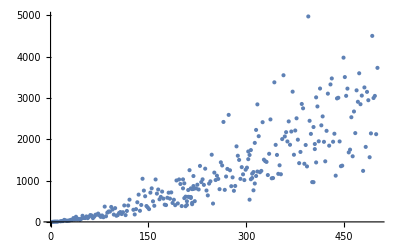

```mathematica
ListPlot[rawData]
```

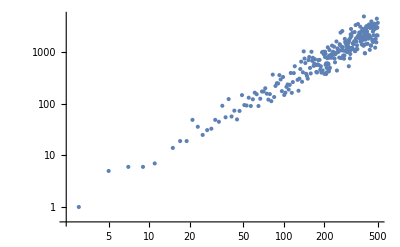

```mathematica
ListLogLogPlot[rawData]
```

```mathematica
Clear[x]
```

```mathematica
FindFit[Log[rawData],a+df *x,{a,df},x]
```

{a→-1.29869,df→1.48533}

```mathematica
lm=LinearModelFit[Log[rawData],x,x]
```

FittedModel[…]

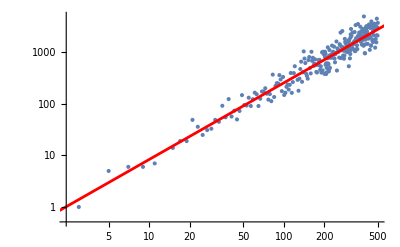

d_f=1.48533±0.0237014
Result from the litterature: UNKOWN

```mathematica
Show[ListLogLogPlot[rawData],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
]
Print[ "d_f=",df/.FindFit[Log[rawData],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature: UNKOWN"]
```

### Drop the first few

```mathematica
joinedData=rawData;
```

```mathematica
dropped=Drop[joinedData,30];
FindFit[Log[dropped],a+df *x,{a,df},x]
lm=LinearModelFit[Log[dropped],x,x]
```

{a→-1.52431,df→1.52505}

FittedModel[…]

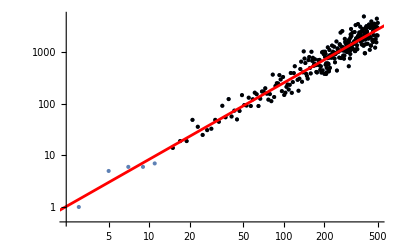

d_f=1.48351±0.0280377
Result from the litterature: UNKNOWN

```mathematica
dropped=Drop[Drop[joinedData,5],0];
lm=LinearModelFit[Log[dropped],x,x];
Show[ListLogLogPlot[joinedData],ListLogLogPlot[dropped,PlotStyle->Black],
Plot[lm[x],{x,0,1000},PlotStyle->Red]
]
Print[ "d_f=",df/.FindFit[Log[dropped],a+df *x,{a,df},x],"±",lm["ParameterErrors"][[2]],"
Result from the litterature: UNKNOWN"]
```

```mathematica
lm["ParameterErrors"]
```

{0.169973,0.0312594}

### Get stdDev by using Kay’s method

#### All the data

```mathematica
rawData=joinedData;
joinedData=rawData;
```

```mathematica
empirical=Module[{sampled,lm,a,df,x,slopeData,meanSlope,stdDevSlope},

slopeData=Table[
sampled=RandomSample[Log[joinedData],Floor[Length[joinedData]/2]];

lm=FindFit[sampled,a+df *x,{a,df},x];

df/.lm
,{i,1,10000}];

meanSlope=Mean[slopeData];
stdDevSlope=StandardDeviation [slopeData];

Return[{meanSlope,stdDevSlope}];
];
```

Return[{1.48604,0.0235037}]

```mathematica
empirical
```

{1.48604,0.0235037}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x];
lm["ParameterErrors"]
{meanExact,stdDevExact}={(lm["ParameterTable"]//Normal)[[1,3,2]],lm["ParameterErrors"][[2]]}
dfExact=df/.FindFit[joinedData,a+df *x,{a,df},x]
{mantExact,expExact}=myMantissaExponent[meanExact]
{mantstdDevExact,expstdDevExact}=MantissaExponent[stdDevExact]
```

{0.126971,0.0237014}

{1.48533,0.0237014}

6.19169

Set::shape: Lists {mantExact,expExact} and myMantissaExponent[1.48533] are not the same shape.

myMantissaExponent[1.48533]

{0.237014,-1}

```mathematica
{mantEmp,expEmp}=myMantissaExponent[empirical[[1]]]
```

Set::shape: Lists {mantEmp,expEmp} and myMantissaExponent[1.48604] are not the same shape.

myMantissaExponent[1.48604]

```mathematica
Print[" The exact value of the slope from the data is (",mantExact,"±",mantstdDevExact,")×",Superscript[10,MantissaExponent[meanExact][[2]]-1], "
 While, by using Kay's procedure, we get (",mantEmp,"±",MantissaExponent[empirical[[2]]][[1]],")×",Superscript[10,expEmp]]
```

The exact value of the slope from the data is (mantExact±0.237014)×10^0
 While, by using Kay's procedure, we get (mantEmp±0.235037)×10^expEmp

#### On dropped data

```mathematica
joinedData=dropped=Drop[rawData,15];
```

```mathematica
empirical=Module[{sampled,lm,a,df,x,slopeData,meanSlope,stdDevSlope},

slopeData=Table[
sampled=RandomSample[Log[joinedData],Floor[Length[joinedData]/2]];

lm=FindFit[sampled,a+df *x,{a,df},x];

df/.lm
,{i,1,10000}];

meanSlope=Mean[slopeData];
stdDevSlope=StandardDeviation [slopeData];

Return[{meanSlope,stdDevSlope}];
];
```

Return[{1.48538,0.0347865}]

```mathematica
empirical
```

{1.48538,0.0347865}

```mathematica
lm=LinearModelFit[Log[joinedData],x,x];
lm["ParameterErrors"]
{meanExact,stdDevExact}={(lm["ParameterTable"]//Normal)[[1,3,2]],lm["ParameterErrors"][[2]]}
dfExact=df/.FindFit[joinedData,a+df *x,{a,df},x]
{mantExact,expExact}=myMantissaExponent[meanExact]
{mantstdDevExact,expstdDevExact}=MantissaExponent[stdDevExact]
```

{0.189115,0.0345711}

{1.48544,0.0345711}

6.42888

Set::shape: Lists {mantExact,expExact} and myMantissaExponent[1.48544] are not the same shape.

myMantissaExponent[1.48544]

{0.345711,-1}

```mathematica
{mantEmp,expEmp}=myMantissaExponent[empirical[[1]]]
```

Set::shape: Lists {mantEmp,expEmp} and myMantissaExponent[1.48538] are not the same shape.

myMantissaExponent[1.48538]

```mathematica
Print[" The exact value of the slope from the data is (",mantExact,"±",mantstdDevExact,")×",Superscript[10,MantissaExponent[meanExact][[2]]-1], "
 While, by using Kay's procedure, we get (",mantEmp,"±",MantissaExponent[empirical[[2]]][[1]],")×",Superscript[10,expEmp]]
```

The exact value of the slope from the data is (mantExact±0.345711)×10^0
 While, by using Kay's procedure, we get (mantEmp±0.347865)×10^expEmp